```mathematica
Needs["Notation`"]
```

```mathematica
Quiet[{
Symbolize[Subscript[ak, x]],Symbolize[Subscript[ak, y]],Symbolize[ϵ_+],Symbolize[ϵ_-],Symbolize[Subscript[t, 1]],Symbolize[Subscript[t, 2]],Symbolize[ϵ],
}];
```

```mathematica
Π= Pi;
```

Square Lattice

```mathematica
ϵ:= -2t (Cos[Subscript[ak, x]] + Cos[Subscript[ak, y]])
```

```mathematica
t:=1
```

```mathematica
Plot3D[ϵ,{Subscript[ak, x] , -Π, +Π},{Subscript[ak, y], -Π , +Π },AxesLabel->(Style[#,FontSize->18]&)/@{
"ak_x","ak_y","ϵ/t"}, Axes->True]
```

-Graphics3D-

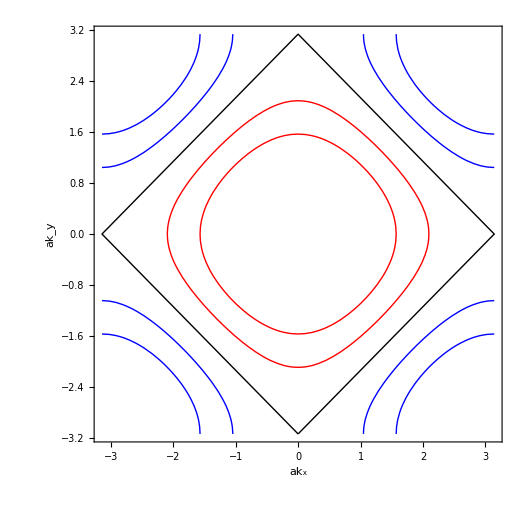

```mathematica
ContourPlot[ϵ,{Subscript[ak, x] , -Π, +Π},{Subscript[ak, y], -Π , +Π },AxesLabel->(Style[#,FontSize->18]&)/@{
"ak_x","ak_y"}, Contours->{-2, -1, 0, 1,2}, ContourStyle->{Red, Red ,Black, Blue, Blue}, ContourShading->None,Ticks->False]
```

```mathematica
PlotFermiSurfaceSpecific[,]
```

```mathematica
Subscript[t, 1]= 1;
```

```mathematica
SubPlus[ϵ]:= Subscript[t, 1] √(1 + 4Cos[Subscript[ak, x]/2]Cos[(√3 Subscript[ak, y])/2] + 4Cos[Subscript[ak, x]/2]^2)
```

```mathematica
SubMinus[ϵ] := - SubPlus[ϵ]
```

```mathematica
BrillouinZone[m_] := Function[{Subscript[ak, x],Subscript[ak, y]},-m⩽(√3 Subscript[ak, x] + Subscript[ak, y]) ⩽+m  && -m⩽(-√3 Subscript[ak, x] + Subscript[ak, y]) ⩽+m  &&-m⩽2(Subscript[ak, y]) ⩽+m];
NotBrillouinZone[m_] := Function[{Subscript[ak, x],Subscript[ak, y]},Not[BrillouinZone[m][Subscript[ak, x],Subscript[ak, y]]]];
```

```mathematica
PlotDispersion[]:= (Show[
Plot3D[SubPlus[ϵ],{Subscript[ak, x] , -2Π, +2Π},{Subscript[ak, y], -2Π , +2Π },PlotTheme->"Default"] ,
Plot3D[SubMinus[ϵ],{Subscript[ak, x] , -2Π, +2Π},{Subscript[ak, y], -2Π , +2Π },PlotTheme->"Classic"] ,
PlotRange->All
])
```

```mathematica
PlotFermiSurface[reg_]:= (ContourPlot[SubMinus[ϵ],{Subscript[ak, x] , -2Π, +2Π},{Subscript[ak, y], -2Π , +2Π },
RegionFunction->reg, PlotTheme->"Classic", PlotLegends->Automatic])
```

```mathematica
PlotFermiSurfaceSpecific[specific_, colors_]:= ContourPlot[SubMinus[ϵ],{Subscript[ak, x] , -2Π, +2Π},{Subscript[ak, y], -2Π , +2Π },
Contours->specific, ContourStyle->colors, ContourShading->None]
```

```mathematica
PlotDispersion[]
```

-Graphics3D-

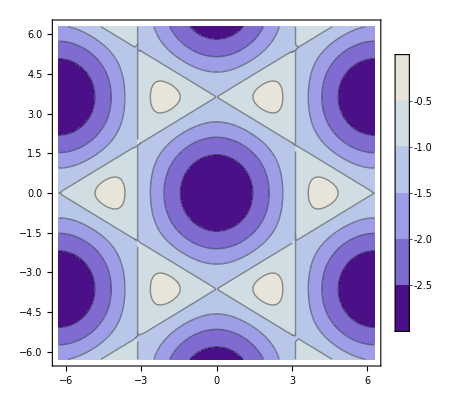

```mathematica
PlotFermiSurface[True]
```

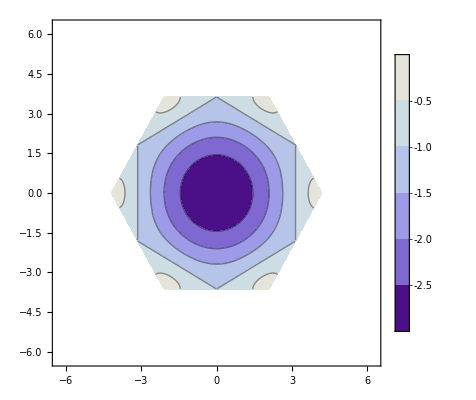

```mathematica
PlotFermiSurface[BrillouinZone[4/(√3)Pi]]
```

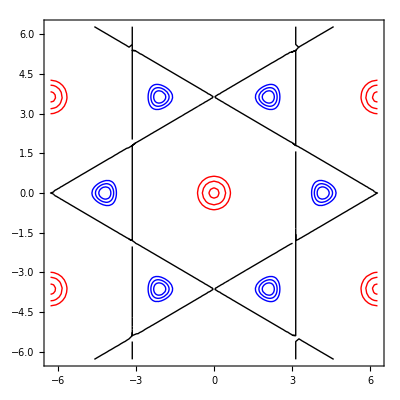

```mathematica
PlotFermiSurfaceSpecific[{-2.99, -2.95, -2.9, -1, -0.2, -0.3, -0.4},{Red, Red, Red ,Black, Blue, Blue ,Blue}]
```